```mathematica
(*Variation in the argument of periapsis*)
argPeriapsisX[f_]:=-Sin[f]/(1+Cos[f]);
argPeriapsisY[f_]:=Cos[f]/(1+Cos[f]);

(*Variation in the time of periapsis*)
timePeriapsisX[f_]:=-Sin[f];
timePeriapsisY[f_]:=1+Cos[f];

(*Variation in the periapsis distance*)
periapsisDistX[f_]:=2-Cos[f];
periapsisDistY[f_]:=-Cos[f] Tan[f/2];

(*Variation in the eccentricity at fixed periapsis*)
eccentricityX[f_]:=(8+12 Cos[f]) Tan[f/4]^4;
eccentricityY[f_]:=(35 Sin[f]-2 Sin[2 f]+3 Sin[3 f])/(1+Cos[f])^2;
```

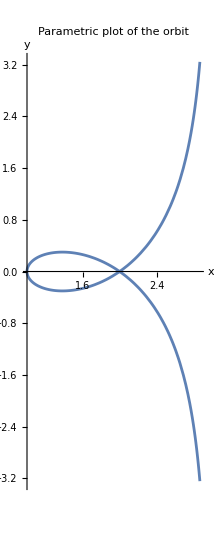

```mathematica
(*Parameters for the problem*)rp=1; (*distance of closest approach*)
G=1;  (*gravitational constant*)
M=1;  (*mass of the central body*)
t0 := -30
t1 := 30

(*Equation (11) solving numerically for anomaly f given time t*)
sol=NDSolve[{Derivative[1][f][t]==Sqrt[2] (1+Cos[f[t]])^2/4,f[0]==0},f,{t,t0,t1}];

(*Extract the solution for f as a function of t*)
fsol[t_]:=f[t]/. sol[[1]];

(*Parametric plot based on equation (15)*)
ParametricPlot[{periapsisDistX[fsol[t]],periapsisDistY[fsol[t]]},{t,t0,t1},PlotRange->All,AxesLabel->{"x","y"},PlotLabel->"Parametric plot of the orbit"]
```

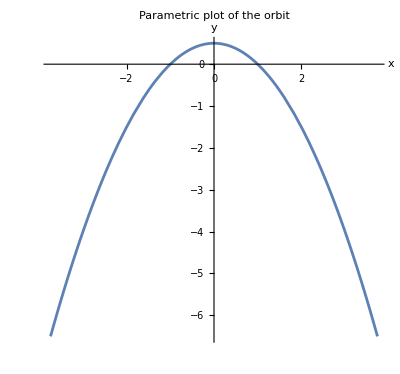

```mathematica
ParametricPlot[{argPeriapsisX[fsol[t]],argPeriapsisY[fsol[t]]},{t,t0,t1},PlotRange->All,AxesLabel->{"x","y"},PlotLabel->"Parametric plot of the orbit"]
```

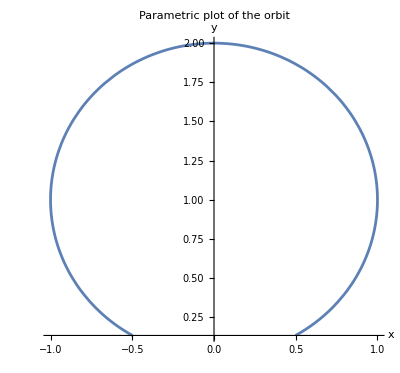

```mathematica
ParametricPlot[{timePeriapsisX[fsol[t]],timePeriapsisY[fsol[t]]},{t,t0,t1},PlotRange->All,AxesLabel->{"x","y"},PlotLabel->"Parametric plot of the orbit"]
```